```mathematica
a =.
x =.
filter[x_, a_] = LanczosWindow[x/(2a)]*Sinc[π*x];
Dynamic[Plot3D[filter[Sqrt[x^2+y^2],3],{x,-5,5},{y,-5,5}, PlotRange->Full]]
```

```mathematica
Dynamic[a]
Slider[Dynamic[a], {0,10}]
```

```mathematica
table = Table[{{x}, filter[x,3]},{x,-10,10,0.5}]
fun = Interpolation[table, Method->"Spline"]
```

{{{-10.},0.},{{-9.5},0.},{{-9.},0.},{{-8.5},0.},{{-8.},0.},{{-7.5},0.},{{-7.},0.},{{-6.5},0.},{{-6.},0.},{{-5.5},0.},{{-5.},0.},{{-4.5},0.},{{-4.},0.},{{-3.5},0.},{{-3.},1.51957×10^-33},{{-2.5},0.0243171},{{-2.},-1.61188×10^-17},{{-1.5},-0.135095},{{-1.},3.22376×10^-17},{{-0.5},0.607927},{{0.},1.},{{0.5},0.607927},{{1.},3.22376×10^-17},{{1.5},-0.135095},{{2.},-1.61188×10^-17},{{2.5},0.0243171},{{3.},1.51957×10^-33},{{3.5},0.},{{4.},0.},{{4.5},0.},{{5.},0.},{{5.5},0.},{{6.},0.},{{6.5},0.},{{7.},0.},{{7.5},0.},{{8.},0.},{{8.5},0.},{{9.},0.},{{9.5},0.},{{10.},0.}}

InterpolatingFunction[{{-10., 10.}}, <>]

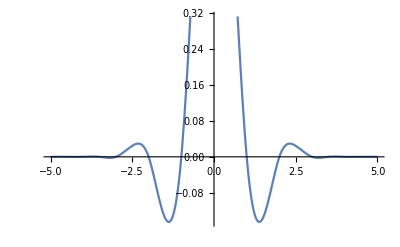

```mathematica
Plot[fun[x], {x, -5, 5}]
```

```mathematica
tab = Flatten[Table[{{x,y}, filter[x,3]*filter[y,3], Limit[Limit[D[filter[k,3] * filter[j,3],{{k,j}}],k->x], j-> y]},{x,-1,1,1},{y,-1,1,1}],1]
```

{{{-1,-1},0,{0,0}},{{-1,0},0,{(3 √3)/(2 π),0}},{{-1,1},0,{0,0}},{{0,-1},0,{0,(3 √3)/(2 π)}},{{0,0},1,{0,0}},{{0,1},0,{0,-(3 √3)/(2 π)}},{{1,-1},0,{0,0}},{{1,0},0,{-(3 √3)/(2 π),0}},{{1,1},0,{0,0}}}

```mathematica
poly = Simplify[InterpolatingPolynomial[tab,{x,y}]]
surfplot=Plot3D[{poly+1, filter[x,3] * filter[y,3]}, {x,-1.5, 1.5}, {y, -1.5,1.5}];
xplot = Plot[{poly /.y->0, filter[x,3] * filter[0,3]}, {x,-1.5, 1.5}];
yplot = Plot[{poly/.x->0, filter[0,3] * filter[y,3]}, {y,-1.5, 1.5}];
```

-((-1+x^2) (-1+y^2) (4 π (-1+x^2+y^2)-3 √3 (x^2+y^2)))/(4 π)

```mathematica
GraphicsGrid[{{surfplot}, {xplot, yplot}}]
```

-Graphics-

```mathematica
Clear[u,v, func]
generatePoly[f_,val_, i_, j_]:=Module[{func, tab},
func[x_,y_]:=f/.{val[[1]]->x, val[[2]]->y};
tab = Flatten[Table[{{x1,y1}, func[x1,y1], Limit[Limit[D[func[u,v],{{u,v}}],u->x1], v-> y1]},{x1,i-1,i+1,1},{y1,j-1,j+1,1}],1];
InterpolatingPolynomial[tab,{x1,y1}];
tab
]
```

```mathematica
generatePoly[filter[x,3] * filter[y,3], {x,y}, 0, 0]
```

{{{-1,-1},0,{0,0}},{{-1,0},0,{(3 √3)/(2 π),0}},{{-1,1},0,{0,0}},{{0,-1},0,{0,(3 √3)/(2 π)}},{{0,0},1,{0,0}},{{0,1},0,{0,-(3 √3)/(2 π)}},{{1,-1},0,{0,0}},{{1,0},0,{-(3 √3)/(2 π),0}},{{1,1},0,{0,0}}}

```mathematica
generatePoly[x+3y,{x,y},1,2]
```

x1+3 y1

```mathematica
coefficients = "-0.01160642, -0.00050091, 0.02300606, 0.00180120, -0.00170263,
       0.00180120, 0.02300606, -0.00050091, -0.01160642, -0.00050091,
       0.03680613, 0.01481606, -0.08703264, 0.04975545, -0.08703264,
       0.01481606, 0.03680613, -0.00050091, 0.02300606, 0.01481606,
       -0.09597746, 0.25609217, 0.06852937, 0.25609217, -0.09597746,
       0.01481606, 0.02300606, 0.00180120, -0.08703264, 0.25609217,
       -0.34959090, -0.56486890, -0.34959090, 0.25609217, -0.08703264,
       0.00180120, -0.00170263, 0.04975545, 0.06852937, -0.56486890,
       2.94628335, -0.56486890, 0.06852937, 0.04975545, -0.00170263,
       0.00180120, -0.08703264, 0.25609217, -0.34959090, -0.56486890,
       -0.34959090, 0.25609217, -0.08703264, 0.00180120, 0.02300606,
       0.01481606, -0.09597746, 0.25609217, 0.06852937, 0.25609217,
       -0.09597746, 0.01481606, 0.02300606, -0.00050091, 0.03680613,
       0.01481606, -0.08703264, 0.04975545, -0.08703264, 0.01481606,
       0.03680613, -0.00050091, -0.01160642, -0.00050091, 0.02300606,
       0.00180120, -0.00170263, 0.00180120, 0.02300606, -0.00050091,
       -0.01160642";
interpreter = Interpreter[DelimitedSequence["Real"]];
coefficients = Partition[interpreter[coefficients],9];
```

```mathematica
knotsx = "-3.00000000, -3.00000000, -3.00000000, -3.00000000, -2.00000000,
        -1.00000000, 0.00000000, 1.00000000, 2.00000000, 3.00000000,
        3.00000000, 3.00000000, 3.00000000";
knotsy = "-3.00000000, -3.00000000, -3.00000000, -3.00000000, -2.00000000,
        -1.00000000, 0.00000000, 1.00000000, 2.00000000, 3.00000000,
        3.00000000, 3.00000000, 3.00000000";
knotsx = interpreter[knotsx];
knotsy = interpreter[knotsy];
knots = Partition[Riffle[knotsx, knotsy],2];
```

```mathematica
Clear[bsplinefun];
bsplinefun[x_,y_]:=Sum[coefficients[[n+1,m+1]]*PiecewiseExpand[BSplineBasis[{3,knots[[All,1]]},n,x]] * PiecewiseExpand[BSplineBasis[{3,knots[[All,2]]},m,y]], {n,0,8},{m,0,8}];
```

```mathematica
Plot3D[{bsplinefun[x,y]},{x,-4,4},{y,-4,4}, PlotRange->All]
```

-Graphics3D-

```mathematica
Simplify[bsplinefun[x,y], Assumptions->{x<2, x>1,y<2,y>1}]
```

5.9406-9.19367 y+4.50761 y^2-0.713145 y^3+x^3 (-0.713145+0.285604 y+0.263619 y^2-0.108058 y^3)+x^2 (4.50761-3.62158 y+0.0968378 y^2+0.263619 y^3)+x (-9.19367+10.8727 y-3.62158 y^2+0.285604 y^3)

```mathematica
Clear[filterPiece,x,y,i,j];
filterPiece[x_, y_, i_, j_] := Simplify[bsplinefun[u+i,v+j],Assumptions->{u<1, u>0,v<1,v>0}]/.{u->x,v->y};
```

```mathematica
Simplify[filterPiece[x,y,0,0]]
```

1.01956-2.26901 y^2+1.23853 y^3+x^2 (-2.26901+3.72643 y^2-1.86783 y^3)+x^3 (1.23853-1.86783 y^2+0.909623 y^3)

```mathematica
intFilterPieceX[x_,y_,i_,j_] := Integrate[filterPiece[u,y,i,j],{u,0,x}]
```

```mathematica
intFilterPieceX[0.3,0.6,1,1]
```

-0.00513243

```mathematica
intFilterPieceX[x,y,0,0]
```

1/3 x^3 (-2.26901+3.72643 y^2-1.86783 y^3)+1/4 x^4 (1.23853-1.86783 y^2+0.909623 y^3)+x (1.01956-2.26901 y^2+1.23853 y^3)

```mathematica
line[t_]:={p0x+(p1x-p0x)*t, p0y+(p1y-p0y)*t}
```

```mathematica
Clear[poly];
poly[i_,j_] := Integrate[intFilterPieceX[line[t][[1]],line[t][[2]],i,j]*D[line[t],t][[2]],{t,0,1}]
```

```mathematica
CoefficientArrays[Chop[poly[0,0], 0.01],{p0x,p0y,p1x,p1y}]
```

{0,SparseArray[<0>, {4}],SparseArray[<4>, {4, 4}],SparseArray[<0>, {4, 4, 4}],SparseArray[<16>, {4, 4, 4, 4}],SparseArray[<20>, {4, 4, 4, 4, 4}],SparseArray[<16>, {4, 4, 4, 4, 4, 4}],SparseArray[<36>, {4, 4, 4, 4, 4, 4, 4}],SparseArray[<15>, {4, 4, 4, 4, 4, 4, 4, 4}]}

```mathematica
CForm[Simplify[Chop[poly[2,2], 0.01]]]
```

((-p0y + p1y)*(Power(p0x,4)*(-0.04592623304687504*Power(p0y,3) + 
          Power(p0y,2)*(0.1555384159821438 - 0.01968267130580248*p1y) + 
          p0y*(-0.1088925334374995 + 0.05184613866071397*p1y) + 
          (-0.021778506687499977 + 0.01036922773214305*p1y)*p1y) + 
       Power(p1x,2)*(-0.05955519374999996 - 0.02177850668749992*Power(p0y,3) + 
          Power(p0y,2)*(0.03789724687500001 - 0.06533552006249999*p1y) + 
          0.07657294781249999*p1y + 0.22738348125000002*Power(p1y,2) - 
          0.21778506687499996*Power(p1y,3) + 
          p0y*(0.025524315937499986 + 0.11369174062499998*p1y - 
             0.13067104012499997*Power(p1y,2))) + 
       p1x*(0.040769151249999996 + Power(p0y,2)*
           (0.049187000625000005 - 0.015130905750000007*p1y) - 0.11911038749999998*p1y + 
          0.14756100187499996*Power(p1y,2) - 0.030261811500000003*Power(p1y,3) + 
          p0y*(-0.05955519375 + 0.09837400124999995*p1y - 
             0.022696358624999982*Power(p1y,2))) + 
       Power(p1x,4)*(0.010369227732142883*Power(p0y,2) + 
          p1y*(-0.10889253343749998 + 0.15553841598214285*p1y - 
             0.04592623304687499*Power(p1y,2)) + 
          p0y*(-0.02177850668749999 + 0.05184613866071425*p1y - 
             0.01968267130580359*Power(p1y,2))) + 
       Power(p1x,3)*(0.04918700062499995 + 0.010369227732142827*Power(p0y,3) + 
          Power(p0y,2)*(-0.041988590874999954 + 0.04147691092857153*p1y) + 
          0.15158898750000002*p1y - 0.4198859087499999*Power(p1y,2) + 
          0.2073845546428571*Power(p1y,3) + 
          p0y*(0.037897246874999985 - 0.16795436350000015*p1y + 
             0.1036922773214285*Power(p1y,2))) + 
       Power(p0x,3)*(0.04918700062499995 + 
          Power(p0y,3)*(0.20738455464285632 - 0.02624356174107101*p1x) + 
          Power(p0y,2)*(-0.4198859087500013 + 
             p1x*(0.10369227732142794 - 0.026243561741073673*p1y) + 
             0.10369227732142794*p1y) + 
          (0.03789724687499996 - 0.04355701337499984*p1x)*p1y + 
          (-0.041988590874999954 + 0.031107683196428093*p1x)*Power(p1y,2) + 
          0.010369227732142827*Power(p1y,3) + 
          p0y*(0.15158898750000005 - 0.1679543635000016*p1y + 
             0.0414769109285722*Power(p1y,2) + 
             p1x*(-0.0871140267499999 + 0.0829538218571444*p1y - 
                0.015746137044642783*Power(p1y,2)))) + 
       Power(p0x,2)*(-0.05955519374999996 + 
          Power(p0y,3)*(-0.217785066874999 + 0.10369227732142794*p1x - 
             0.013121780870536837*Power(p1x,2)) + 
          Power(p0y,2)*(0.22738348124999996 + 
             Power(p1x,2)*(0.062215366392857074 - 0.023619205566963952*p1y) + 
             p1x*(-0.2519315452499984 + 0.12443073278571415*p1y) - 
             0.13067104012500041*p1y) + 0.025524315937500014*p1y + 
          0.03789724687500001*Power(p1y,2) - 0.021778506687500032*Power(p1y,3) + 
          Power(p1x,2)*p1y*(-0.06533552006249999 + 0.062215366392857296*p1y - 
             0.013121780870535671*Power(p1y,2)) + 
          p1x*(0.04918700062499995 + 0.07579449375000002*p1y - 
             0.12596577262499986*Power(p1y,2) + 0.04147691092857153*Power(p1y,3)) + 
          p0y*(0.07657294781249999 + 0.11369174062499954*p1y - 
             0.0653355200625001*Power(p1y,2) + 
             Power(p1x,2)*(-0.0653355200625001 + 0.09332304958928406*p1y - 
                0.023619205566964396*Power(p1y,2)) + 
             p1x*(0.11369174062499954 - 0.2519315452500015*p1y + 
                0.09332304958928406*Power(p1y,2)))) + 
       p0x*(0.040769151249999996 + Power(p0y,3)*
           (-0.030261811499999958 - 0.0871140267499999*p1x + 
             0.0414769109285722*Power(p1x,2)) + 
          Power(p0y,2)*(0.14756100187499976 + 
             p1x*(0.11369174062499954 - 0.1306710401250002*p1y) + 
             Power(p1x,3)*(0.031107683196428093 - 0.015746137044643227*p1y) + 
             Power(p1x,2)*(-0.12596577262500075 + 0.09332304958928406*p1y) - 
             0.02269635862500008*p1y) - 0.05955519375*p1y + 
          0.04918700062499998*Power(p1y,2) + 
          Power(p1x,3)*p1y*(-0.08711402674999996 + 0.1036922773214285*p1y - 
             0.026243561741071397*Power(p1y,2)) + 
          p1x*(-0.059555193749999985 + 0.05104863187499997*p1y + 
             0.11369174062499998*Power(p1y,2) - 0.08711402674999996*Power(p1y,3)) + 
          Power(p1x,2)*(0.04918700062499995 + 0.11369174062499998*p1y - 
             0.25193154525000017*Power(p1y,2) + 0.1036922773214285*Power(p1y,3)) + 
          p0y*(-0.11911038749999998 + 0.09837400125000001*p1y - 
             0.015130905750000007*Power(p1y,2) + 
             p1x*(0.05104863187500003 + 0.15158898750000005*p1y - 
                0.13067104012499997*Power(p1y,2)) + 
             Power(p1x,3)*(-0.043557013375000064 + 0.08295382185714306*p1y - 
                0.026243561741071342*Power(p1y,2)) + 
             Power(p1x,2)*(0.07579449375000002 - 0.2519315452499997*p1y + 
                0.12443073278571459*Power(p1y,2))))))/12.

```mathematica
testknots={-3,-3,-3,-3,-2,-1,0,1,2,3,3,3,3}
PiecewiseExpand[BSplineBasis[{3,testknots},1,x]]
```

{-3,-3,-3,-3,-2,-1,0,1,2,3,3,3,3}

Piecewise[{{1/4 (-1-3 x-3 x^2-x^3), -2≤x≤-1}, {1/4 (63+93 x+45 x^2+7 x^3), -3≤x<-2}, {0, True}}]